```mathematica
ClearAll["Global`*"];
result=Import[FileNameJoin[{NotebookDirectory[],"dft.dat"}]];
input=Import[FileNameJoin[{NotebookDirectory[],"original.dat"}]];
```

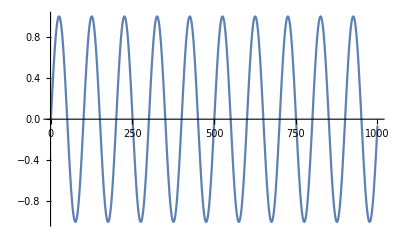

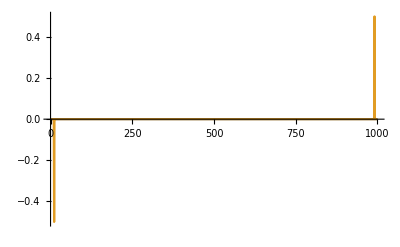

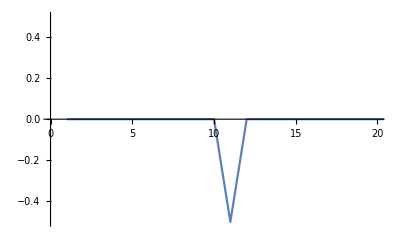

```mathematica
ListPlot[Transpose[input],Joined->True]
ListPlot[Transpose[result],Joined->True,PlotRange->All]
ListPlot[Transpose[result][[2]],Joined->True,PlotRange->{{0,20},All}]
```

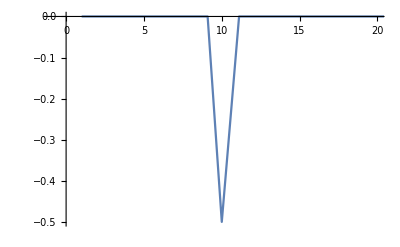

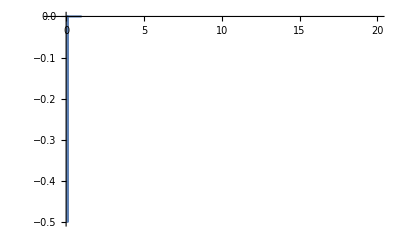

```mathematica
T0=150;

omega[n_]:=2π*n/T0;
freq[n_]:=n/T0;
period[n_]:=1/freq[n];
ListPlot[Table[{period[n],Transpose[result][[2]][[n+1]]},{n,1,100}],Joined->True,PlotRange->{{-1,20},All}]
ListPlot[Table[{freq[n],Transpose[result][[2]][[n+1]]},{n,1,100}],Joined->True,PlotRange->{{-1,20},All}]
```